General::munfl: (-7.70763×10^-105)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.72368×10^-109)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.89494×10^-113)^3 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

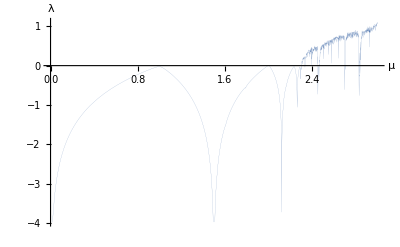

```mathematica
λ[r_]:=Module[{f,l},f[x_]:=r x -(1+r)x^3;
l[x_]:=Log[Abs[r-3(r+1)x^2]];
Mean[l[NestList[f,0.1,1*^2]]]];
Plot[λ[r],{r,0,3},PlotStyle->Thickness[.0001],AxesLabel->{"μ","λ"}]
```

```mathematica
Export["D:\\school_work\\thesis\\presentation\\figures\\lyapunov.pdf",%32]
```

D:\school_work\thesis\presentation\figures\lyapunov.pdf